Benford’s law describes the relative frequence of the lead digit of numbers from real-world data-sets that contain data across several orders of magnitude. Numbers will start with the digit 1 about 30% of the time.

The following code uses the Wolfram Language command BenfordDistribution to compare his prediction to the sizes of files in a filesystem.

First collect all the file names that you are interested in.

```mathematica
files=FileNames[All,"/home/jmartin/",7];
```

```mathematica
files
```

```mathematica
FileNames[]
```

{AddOns,BackupDir-65221,Configuration,.CreationID,Documentation,Executables,.InstallTemp-65221,LICENSE.txt,.Revision,SystemFiles,.VersionID}

```mathematica
SetDirectory[$InstallationDirectory]
```

/usr/local/Wolfram/Wolfram/14.2

Now calculated the lead digit of the FileByteCount for each file (discarding folders and empty files).

```mathematica
digitCounts=Counts[First[IntegerDigits[#]]&/@DeleteCases[Quiet[FileByteCount/@files],$Failed|0]];
digitFrequencies=digitCounts/Total[digitCounts];
```

Now use BenfordDistribution to generate the predicted proportions.

```mathematica
predictions=PDF[BenfordDistribution[10],Range[9]];
```

Finally visualize the two data sets

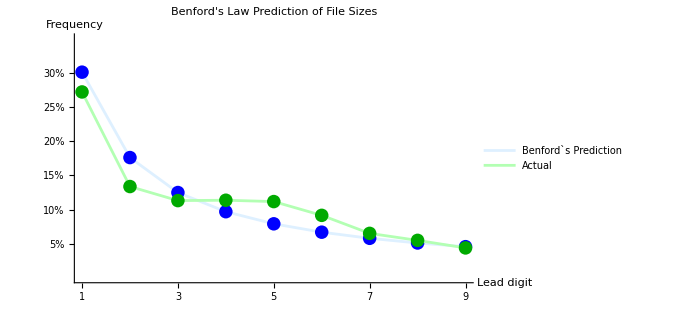

```mathematica
Show[
ListLinePlot[Legended[predictions,"Benford`s\nPrediction"],PlotStyle->LightBlue,MeshStyle->Blue,Mesh->All,AxesLabel->{"Lead digit","Frequency"},PlotLabel->"Benford's Law Prediction of File Sizes",Ticks->{Range[9],Table[{i,PercentForm[i]},{i,0.05,0.3,0.05}]}],

ListLinePlot[Legended[KeySort[digitFrequencies],"Actual"],PlotStyle->Lighter[Green,0.7],MeshStyle->Darker[Green],Mesh->All],ImageSize->500,PlotRange->{0,0.35}]
```

Number of files considered:

```mathematica
Total[digitCounts]
```

371671